# HyperBloch package tutorial

## Haldane model; NNN-models

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Haldane model tutorial on the HyperCells&HyperBloch website.  In this tutorial, we will see how to construct Abelian Bloch Hamiltonians for next-nearest-neighbor tessellation (supercell) model graphs  (constructed through HyperBloch’s sister package HyperCells). Specifically, we will consider next-nearest-neighbor terms as small perturbations of an elementary hopping model, which we will extend to a variant of the Haldane model on a hyperbolic lattice. In particular, the general coupling constant assignment strategy, as presented in getting started with the HyperBloch package, will be essential for this tutorial.

## Preliminaries:

### Remarks:

Before using the notebook to the Haldane model tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc
{6,4}-tess-NNN_T2.2_3.hcm
{6,4}-tess-NNN_T2.2_3_sc-T5.4.hcs
{6,4}-tess-NNN_T2.2_3_sc-T9.3.hcs

In case no such files exist in your current directory, please follow the instructions in the  HyperBloch Haldane model tutorial, or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

$Aborted

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Needed functions:

In previous tutorials, such as getting started with the HyperBloch package and HyperBloch Supercells tutorial etc., we have calculated the density of states of various tight-binding models via exact diagonalization and random samples. We predefine a function in order to calculate the eigenvalues for the Abelian Bloch Hamiltonians that we will construct. We  take advantage of the independence of different momentum sectors and parallelize the computation, where we partition the set of Npts into  Nruns subsets:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## (Supercell) model graphs:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

where we consider the unit cell T2.2 as the primitive cell.

### Import (supercell) model graphs:

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NNN_T2.2_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{6,4}-tess-NNN_T2.2_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst= Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Visualize the primitive cell:

Let us visualize the NN and NNN-terms of the graph representation for the next-nearest-neighbor tight-binding model on the primitive cell. They are stored as directed edges, which can be extracted from the model graph as follows:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{{1,1},1,7}},{2,3}{2,1}{1,{{1,2},6,12}},{2,1}{2,3}{1,{{1,3},13,23}},{2,2}{2,4}{1,{{1,4},2,8}},{2,4}{2,2}{1,{{1,5},15,19}},{2,2}{2,1}{1,{{1,6},14,24}},{2,5}{2,3}{1,{{1,7},5,11}},{2,3}{2,5}{1,{{1,8},18,22}},{2,4}{2,6}{1,{{1,9},3,9}},{2,6}{2,4}{1,{{1,10},16,20}},{2,6}{2,5}{1,{{1,11},4,10}},{2,5}{2,6}{1,{{1,12},17,21}},{2,1}{2,4}{2,{1,1,4}},{2,2}{2,6}{2,{1,4,9}},{2,4}{2,5}{2,{1,9,11}},{2,6}{2,3}{2,{1,11,7}},{2,5}{2,1}{2,{1,7,2}},{2,3}{2,2}{2,{1,2,1}},{2,2}{2,3}{2,{2,1,3}},{2,1}{2,5}{2,{2,3,7}},{2,3}{2,6}{2,{2,7,12}},{2,5}{2,4}{2,{2,12,9}},{2,6}{2,2}{2,{2,9,5}},{2,4}{2,1}{2,{2,5,1}},{2,4}{2,1}{2,{3,4,6}},{2,2}{2,3}{2,{3,6,2}},{2,1}{2,5}{2,{3,2,8}},{2,3}{2,6}{2,{3,8,11}},{2,5}{2,4}{2,{3,11,10}},{2,6}{2,2}{2,{3,10,4}},{2,2}{2,6}{2,{4,5,10}},{2,4}{2,5}{2,{4,10,12}},{2,6}{2,3}{2,{4,12,8}},{2,5}{2,1}{2,{4,8,3}},{2,3}{2,2}{2,{4,3,6}},{2,1}{2,4}{2,{4,6,5}}}

The first entry in the edge tags (the nested list above the arrow) indicate the if the edge connects NN-vertices or NNN-vertices, indicated with integers 1 and 2, respectively.   We can visualize the corresponding edges by using the optional argument EdgeFilter of the function ShowCellGraphFalttened. This enables us to visualize edges connecting NN-vertices or NNN-vertices separately:

```mathematica
Row[
Table[
Module[{filterFunction},
filterFunction[edge_,j_]:=If[j<3,edge[[3,1]]==j,edge[[3,1]]<j];
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
Elements-><|
	ShowCellGraphFlattened->{EdgeFilter->(filterFunction[#,j]&)},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->300,
NumberOfGenerations->3]],
{j,3}]]
```

-Graphics--Graphics--Graphics-

## {6,4} NNN tight-binding model:

Before we construct the Haldane model on the {6,4}-lattice, let us consider a more fundamental model in order to get familiar with the procedures to assign coupling constants for next-nearest-neighbor (supercell) model graphs. As such, let us construct an elementary next-nearest-neighbor hopping model.

### Construct Abelian Bloch Hamiltonians:

#### Hopping amplitudes:

In order to construct the Abelian Bloch Hamiltonian, we need to identify the NN and NNN-terms. Once again let us look at the list of edges in the model graph:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{{1,1},1,7}},{2,3}{2,1}{1,{{1,2},6,12}},{2,1}{2,3}{1,{{1,3},13,23}},{2,2}{2,4}{1,{{1,4},2,8}},{2,4}{2,2}{1,{{1,5},15,19}},{2,2}{2,1}{1,{{1,6},14,24}},{2,5}{2,3}{1,{{1,7},5,11}},{2,3}{2,5}{1,{{1,8},18,22}},{2,4}{2,6}{1,{{1,9},3,9}},{2,6}{2,4}{1,{{1,10},16,20}},{2,6}{2,5}{1,{{1,11},4,10}},{2,5}{2,6}{1,{{1,12},17,21}},{2,1}{2,4}{2,{1,1,4}},{2,2}{2,6}{2,{1,4,9}},{2,4}{2,5}{2,{1,9,11}},{2,6}{2,3}{2,{1,11,7}},{2,5}{2,1}{2,{1,7,2}},{2,3}{2,2}{2,{1,2,1}},{2,2}{2,3}{2,{2,1,3}},{2,1}{2,5}{2,{2,3,7}},{2,3}{2,6}{2,{2,7,12}},{2,5}{2,4}{2,{2,12,9}},{2,6}{2,2}{2,{2,9,5}},{2,4}{2,1}{2,{2,5,1}},{2,4}{2,1}{2,{3,4,6}},{2,2}{2,3}{2,{3,6,2}},{2,1}{2,5}{2,{3,2,8}},{2,3}{2,6}{2,{3,8,11}},{2,5}{2,4}{2,{3,11,10}},{2,6}{2,2}{2,{3,10,4}},{2,2}{2,6}{2,{4,5,10}},{2,4}{2,5}{2,{4,10,12}},{2,6}{2,3}{2,{4,12,8}},{2,5}{2,1}{2,{4,8,3}},{2,3}{2,2}{2,{4,3,6}},{2,1}{2,4}{2,{4,6,5}}}

We choose to assign two different symbolic arguments for the NN and NNN contributions:

NN-terms:

```mathematica
nnVec=ConstantArray[h1,12];
```

NNN-terms:

```mathematica
nnnVec=ConstantArray[h2 ,24];
```

The hopping amplitudes can be assigned through an Association, with edges as keys and hopping amplitudes as values:

```mathematica
hoppingVec=Join[nnVec,nnnVec];
hoppingsPC=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVec];
```

#### Hamiltonians:

Once the (supercell) model graphs are imported and the coupling constants are assigned the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,hoppingsPC,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,0&,hoppingsPC,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We choose to treat the next-nearest-neighbor contributions as a weak coupling between sites, as such we set h1 to 1 and h2 to 0.05.

Let us compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{h1->1,h2->0.05},  10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

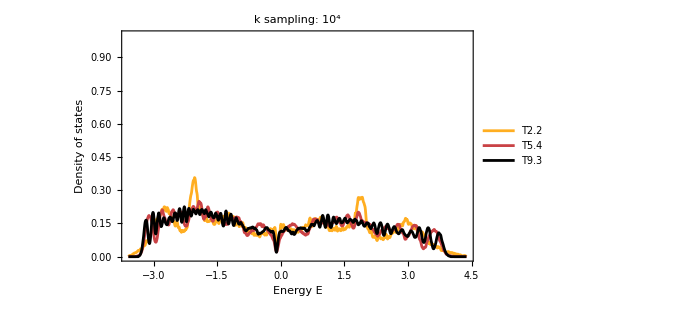

```mathematica
SmoothHistogram[evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 10^4",PlotRange->{0,1},PlotStyle->cLst]
```

## {6,4} Haldane model:

The next-nearest-neighbor tight-binding model can easily be extended to a Haldane model. The directed edges within the (supercell) model graphs are oriented such that a Peierls substitution can be performed with a minor modification. Let’s see how we can appropriately modify the elementary NNN-model.

### Constructing Hamiltonians:

#### Staggered on-site potential:

Since the hyperbolic hexagons have an even number of sides the lattice can be considered as bipartite such that a sublattice mass can be realized by a staggered on-site potential. It is instructive to take a look at the list of vertices in the model graph:

```mathematica
VertexList@pcmodel["Graph"]
```

{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6}}

Comparing the list of vertices with the model representation we have previously visualized, we can assign the staggered on-site potential  ±m as follows:

```mathematica
mVec =m{1,-1,-1,1,1,-1};
onsitePCHaldane=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### Hopping amplitudes:

The Peierls substitution can be performed by multiplying the previously defined constant vector nnnVec by a phase ⅇ^ⅈϕ. The resulting-lattice is threaded by local magnetic fluxes with net zero flux per hyperbolic hexagon:

```mathematica
fp= Exp[ⅈ ϕ];
nnnVecHaldane=fp nnnVec;
```

The new hopping amplitudes can be assigned through an Association, with edges as keys and hopping amplitudes as values:

```mathematica
hoppingVecHaldane=Join[nnVec,nnnVecHaldane];
hoppingsPCHaldane=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVecHaldane];
```

##### Visualize the hyperbolic hexagons:

Let us highlight the central hyperbolic hexagon, which is threaded with net zero flux. The hexagon is associated with a face in the model graph and the corresponding polygon can be extracted through the function  GetCellGraphFace:

```mathematica
face=GetCellGraphFace[pcmodel,pcmodel["Faces"][[1]]];
```

```mathematica
Show[
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
Elements-><|
	ShowCellGraphFlattened->{},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->300,
NumberOfGenerations->3],

Graphics[{Opacity[0],FaceForm[{Darker@Green,Opacity[0.5]}],face}]
]
```

-Graphics-

#### Hamiltonians:

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,onsitePCHaldane,hoppingsPCHaldane,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,onsitePCHaldane,hoppingsPCHaldane,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{h1->1,h2->0.5, m->0,ϕ->π/2},10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

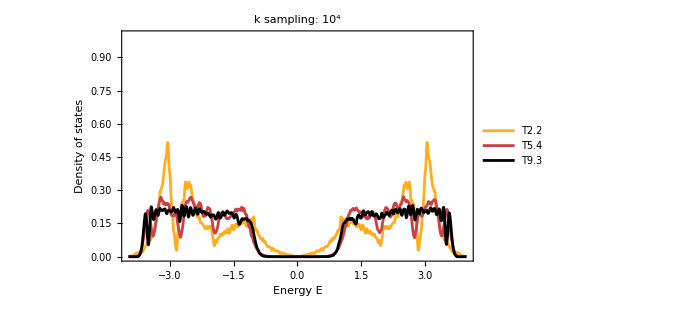

```mathematica
SmoothHistogram[evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 10^4",PlotRange->{0,1},PlotStyle->cLst]
```

```mathematica
NotebookSave[]
```